# GW Spectrum

```mathematica
ClearAll["Global`*"]
```

```mathematica
myTicks[lower_,upper_,step_]:=Flatten[Module[{Local=#,LocalTicks},LocalTicks=Log[10,Range[10^(#-1),10^#,(10^#-10^(#-1))/(10-1)]];
Join[{#,""}&/@Most[LocalTicks],{{Last[LocalTicks],Which[Last[LocalTicks]==0,1,Last[LocalTicks]==1,10,True,Power[10,ToString[Last[LocalTicks]]]],{0.03,0}(*longer ticks*)}}]]&/@Range[lower,upper,step],1];
```

## GW in ultrasound wall speed

### Benchmark 1: mS=10mev, sinθ=2.1×10^-4

```mathematica
Tn=39.619974882131295;
α=0.005770712843595349;
βH=54608227.79597033;
vb=1.;
```

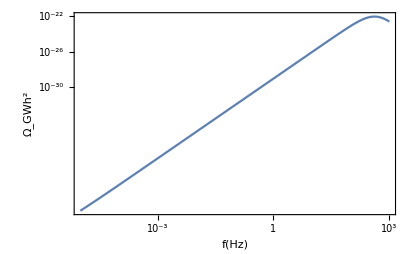

```mathematica
fsou[vb_,βH_,Tn_]:=1.9*10^(-5)*(100/100)^(1/6)*(Tn/100)*(βH)/vb;
κ[α_]:=α/(0.73+0.083Sqrt[α]+α);
Ωsou[f_,vb_,α_,βH_,Tn_]:=2.65*10^(-6)*vb*(100/100)^(1/3)/βH*(κ[α]*α/(1+α))^2*(7^(7/2)*(f/fsou[vb,βH,Tn])^3/(4+3(f/fsou[vb,βH,Tn])^2)^(7/2));
κtur[α_]=.05*κ[α];
(*Plasma turbulence*)
ftur[vb_,βH_,Tn_]=2.7/vb*10^(-5)*βH*(Tn/100)*(100/100)^(1/6);
(*A peak frequency of the turbulence*)
hstar[Tn_]:=16.5*10^(-6)*(Tn/100)*(100/100)^(1/6);
(*Hubble paramter at Subscript[T, n]*)
Ωtur[f_,vb_,α_,βH_,Tn_]:=3.35*10^(-4)/βH*(κtur[α]*α/(1+α))^(3/2)*(100/100)^(1/3)*vb*(f/ftur[vb,βH,Tn])^3/(1+f/(ftur[vb,βH,Tn]))^(11/3)/(1+8*Pi*f/hstar[Tn]);signal=Plot[Log10[Ωsou[10^logf,1.0,α,βH,Tn]+Ωtur[10^logf,1.0,α,βH,Tn]],{logf,-5,3},Axes->None,BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,FrameLabel->{Style["f(Hz)",FontFamily->"Times",FontSize->18],Style["Ω_GWh^2",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]},FrameTicks->{{myTicks[-30,-7,2],None},{myTicks[-6,6,1],None}}]
```

## Observation

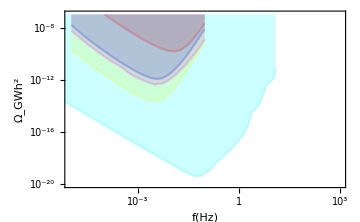

```mathematica
eLISAC4=Import[NotebookDirectory[]<>"data/LISAC4.csv"];
eLISAC3=Import[NotebookDirectory[]<>"data/LISAC3.csv"];
eLISAC2=Import[NotebookDirectory[]<>"data/LISAC2.csv"];
eLISAC1=Import[NotebookDirectory[]<>"data/LISAC1.csv"];
UD=Import[NotebookDirectory[]<>"data/UltimateDecigo-Sachiko.csv"];
eLISAandUD=ListLinePlot[{eLISAC4,eLISAC3,eLISAC2,eLISAC1,UD},Filling->Top,ImageSize->Medium,Axes->None,PlotRange->{{-5,3},{-20,-7}},FrameTicks->{{myTicks[-20,-7,2],None},{myTicks[-6,6,1],None}},FrameTicksStyle->{16,Black,FontFamily->"Times"},FrameLabel->{Style["f(Hz)",FontFamily->"Times",FontSize->18],Style["Ω_GWh^2",FontFamily->"Times",FontSize->18]},PlotStyle->{{RGBColor[1,0,0],Opacity[0.2]},{RGBColor[0,0,1],Opacity[0.2]},{RGBColor[1,0,1],Opacity[0.2]},{RGBColor[1,1,0],Opacity[0.2]},{RGBColor[0,1,1],Opacity[0.2]}},Background->White,LabelStyle->{FontFamily->"Times",FontSize->16},PlotRangePadding->None]
```

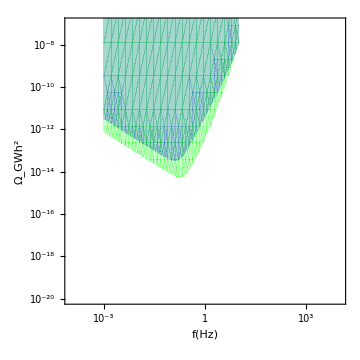

```mathematica
DECIGOandBBO=RegionPlot[{y>Log10[(3*10^17)^2*2*Pi^2/3*(10^f)^3(7.05*10^(-48)*(1+(10^f/7.36)^2)+4.8*10^(-51)/10^(4f)/(1+(10^f/7.36)^2)+5.33*10^(-52)10^(-4f))],y>Log10[(3*10^17)^2*2*Pi^2/3*(10^f)^3(2*10^(-49)*10^(2f)+4.58*10^(-49)+1.26*10^(-51)*10^(-4f))]},{f,-3,1},{y,-30,0},ImageSize->Medium,Axes->None,PlotRange->{{-4,4},{-20,-7}},FrameTicks->{{myTicks[-20,-7,2],None},{myTicks[-6,6,1],None}},FrameTicksStyle->{16,Black,FontFamily->"Times"},FrameLabel->{Style["f(Hz)",FontFamily->"Times",FontSize->16],Style["Ω_GWh^2",FontFamily->"Times",FontSize->16]},Background->White,LabelStyle->{FontFamily->"Times",FontSize->16},PlotRangePadding->None,PlotStyle->{{RGBColor[0,0,1],Opacity[0.2]},{RGBColor[0,1,0],Opacity[0.2]}},BoundaryStyle->None]
```

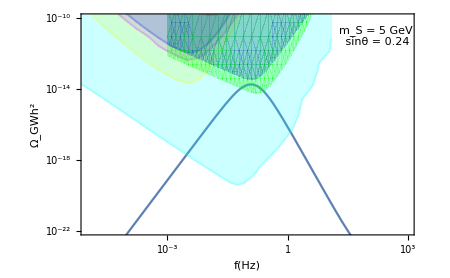

```mathematica
Show[signal,eLISAandUD,DECIGOandBBO,PlotRange->{{-5,3},{-22,-10}},ImageSize->450,Epilog->{Inset[Framed[Style["m_S = 5 GeV\n sinθ = 0.24",FontFamily->"Times",FontSize->14],RoundingRadius->5],{2.2,-11}]}]
```